# Nonstationary simulation, fatty acid synthesis

```mathematica
<<NilssonLab`MetabolicNetwork`
```

```mathematica
<<NilssonLab`ExtremePathways`
<<NilssonLab`IsotopeDistributions`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
```

```mathematica
<<NilssonLab`Visualization`
```

```mathematica
OpenDBConnection[]
```

## Define network model

### Network from database

```mathematica
net=NetworkFromDB["fatty-acid-synthesis"]
```

<MetabolicNetwork, 15 reactions>

```mathematica
Length[Metabolites[net]]
```

26

Stochiometry matrix (metabolites x reactions) for the reversible network

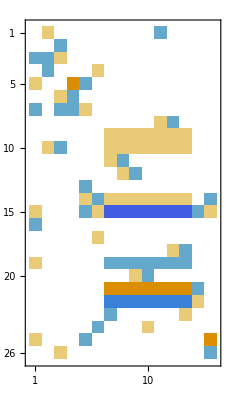

```mathematica
MatrixPlot[Stoichiometry[net]]
```

```mathematica
Union[NonZeroElements[Stoichiometry[net]]]
```

{-3,-2,-1,1,2}

```mathematica
Table[{ReactionID[r],ReactionFormula[net,r]},{r,Reactions[net]}]//TableForm
```

ACCOAC | accoa_c + atp_c + hco3_c ==> adp_c + h_c + malcoa_c + pi_c
ACOATA | accoa_c + ACP_c ==> acACP_c + coa_c
ACS | ac_c + atp_c + coa_c ==> accoa_c + amp_c + ppi_c
ADK1 | amp_c + atp_c ==> 2 adp_c
CELLWORK | adp_c + energy_c + h_c + pi_c ==> atp_c + h2o_c
FA160ACPH | h2o_c + palmACP_c ==> ACP_c + h_c + hdca_c
FAS100ACP | 3 h_c + malcoa_c + 2 nadph_c + ocACP_c ==> co2_c + coa_c + dcaACP_c + h2o_c + 2 nadp_c
FAS120ACP | dcaACP_c + 3 h_c + malcoa_c + 2 nadph_c ==> co2_c + coa_c + ddcaACP_c + h2o_c + 2 nadp_c
FAS140ACP | ddcaACP_c + 3 h_c + malcoa_c + 2 nadph_c ==> co2_c + coa_c + h2o_c + myrsACP_c + 2 nadp_c
FAS160ACP | 3 h_c + malcoa_c + myrsACP_c + 2 nadph_c ==> co2_c + coa_c + h2o_c + 2 nadp_c + palmACP_c
FAS40ACP | acACP_c + 3 h_c + malcoa_c + 2 nadph_c ==> btACP_c + co2_c + coa_c + h2o_c + 2 nadp_c
FAS60ACP | btACP_c + 3 h_c + malcoa_c + 2 nadph_c ==> co2_c + coa_c + h2o_c + hexACP_c + 2 nadp_c
FAS80ACP | 3 h_c + hexACP_c + malcoa_c + 2 nadph_c ==> co2_c + coa_c + h2o_c + 2 nadp_c + ocACP_c
NADPH_REDOX | h_c + nadp_c ==> nadph_c
PPA | h2o_c + ppi_c ==> h_c + 2 pi_c

```mathematica
Table[{MetaboliteShortName[m],Compartment[m],ExchangeStatus[m]},{m,Metabolites[net]}]//TableForm
```

acACP_c | Cytosol | Internal
ac_c | Cytosol | Uptake
accoa_c | Cytosol | Internal
ACP_c | Cytosol | Internal
adp_c | Cytosol | Internal
amp_c | Cytosol | Internal
atp_c | Cytosol | Internal
btACP_c | Cytosol | Internal
co2_c | Cytosol | Release
coa_c | Cytosol | Internal
dcaACP_c | Cytosol | Internal
ddcaACP_c | Cytosol | Internal
energy_c | Cytosol | Uptake
h2o_c | Cytosol | Free
h_c | Cytosol | Free
hco3_c | Cytosol | Uptake
hdca_c | Cytosol | Release
hexACP_c | Cytosol | Internal
malcoa_c | Cytosol | Internal
myrsACP_c | Cytosol | Internal
nadp_c | Cytosol | Internal
nadph_c | Cytosol | Internal
ocACP_c | Cytosol | Internal
palmACP_c | Cytosol | Internal
pi_c | Cytosol | Internal
ppi_c | Cytosol | Internal

#### Generate boundary network

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 9 boundary fluxes>

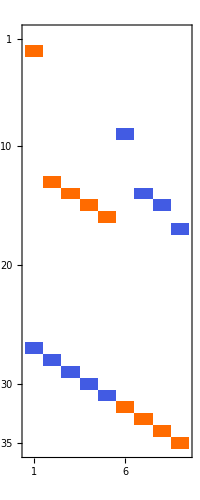

```mathematica
Stoichiometry[bnet]//MatrixPlot
```

```mathematica
BoundaryFluxNames[bnet]
```

{ac_IN,energy_IN,h2o_IN,h_IN,hco3_IN,co2_OUT,h2o_OUT,h_OUT,hdca_OUT}

```mathematica
MetaboliteShortName/@Metabolites[bnet]
```

{acACP_c,ac_c,accoa_c,ACP_c,adp_c,amp_c,atp_c,btACP_c,co2_c,coa_c,dcaACP_c,ddcaACP_c,energy_c,h2o_c,h_c,hco3_c,hdca_c,hexACP_c,malcoa_c,myrsACP_c,nadp_c,nadph_c,ocACP_c,palmACP_c,pi_c,ppi_c,ac_i,energy_i,h2o_i,h_i,hco3_i,co2_o,h2o_o,h_o,hdca_o}

### Extreme points in net flux space

#### Find viable reactions

Note that this works in the space of net fluxes and hence excludes type III pathways!

```mathematica
netFluxMinMax=FindViableReactions[net];
Dimensions[netFluxMinMax]
```

{15,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

2

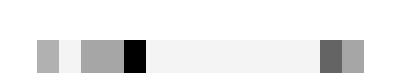

```mathematica
ForwardFlux/@fluxMinMax//ArrayPlot
```

```mathematica
Table[MassBalanceNorm[net,f],{f,fluxMinMax}]//Chop
```

{0,0}

#### Sanity checks

Reactions that cannot carry net flux in the forward direction

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Position[Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],0]]}]//TableForm
```

{}

Reactions that cannot carry net flux in the reverse direction

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]//TableForm
```

{}

Boundary fluxes that are never non-zero

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[h2o,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[h,Output,Boundary]}

### Define true flux vector

```mathematica
fluxRules={"ACS"->{8,0},"ADK1"->{8,0},"PPA"->{8,0},"ACCOAC"->{7,0},"ACOATA"->{1,0},"CELLWORK"->{23,0},"FA160ACPH"->{1,0},"FAS100ACP"->{1,0},"FAS120ACP"->{1,0},"FAS140ACP"->{1,0},"FAS160ACP"->{1,0},"FAS40ACP"->{1,0},"FAS60ACP"->{1,0},"FAS80ACP"->{1,0},"NADPH_REDOX"->{14,0}};
```

```mathematica
trueFlux=FluxState[net,Sequence@@Transpose[(ReactionID/@Reactions[net])/.fluxRules]]
```

<FluxState, 15 reactions, 9 b. exch>

Nonzero metabolite balances

```mathematica
Block[{bal,mi},
bal=MassBalance[net,trueFlux];
mi=Flatten[Position[Chop[bal],Except[0],Heads->False]];
TableForm[bal⟦mi⟧,TableHeadings->{Metabolites[net]⟦mi⟧,None}]]
```

Metabolite[ac,Cytosol,Uptake] | -8
Metabolite[co2,Cytosol,Release] | 7
Metabolite[energy,Cytosol,Uptake] | -23
Metabolite[h2o,Cytosol,Free] | 21
Metabolite[h,Cytosol,Free] | -42
Metabolite[hco3,Cytosol,Uptake] | -7
Metabolite[hdca,Cytosol,Release] | 1

```mathematica
TableForm[
Transpose[{ForwardFlux[trueFlux],ReverseFlux[trueFlux]}],
TableHeadings->{Reactions[net],{"Forward","Reverse"}}]
```

| Forward | Reverse
<Reaction ACCOAC> | 7 | 0
<Reaction ACOATA> | 1 | 0
<Reaction ACS> | 8 | 0
<Reaction ADK1> | 8 | 0
<Reaction CELLWORK> | 23 | 0
<Reaction FA160ACPH> | 1 | 0
<Reaction FAS100ACP> | 1 | 0
<Reaction FAS120ACP> | 1 | 0
<Reaction FAS140ACP> | 1 | 0
<Reaction FAS160ACP> | 1 | 0
<Reaction FAS40ACP> | 1 | 0
<Reaction FAS60ACP> | 1 | 0
<Reaction FAS80ACP> | 1 | 0
<Reaction NADPH_REDOX> | 14 | 0
<Reaction PPA> | 8 | 0

```mathematica
MassBalanceQ[net,trueFlux]
```

True

## Atom map

### Define atom map

All atom transitions for reactions in model

```mathematica
atomMap=RemoveUnreachable[net,AtomMapsFromDB[net,{"C"}]]
```

{<AtomMap, 3 transitions>,<AtomMap, 2 transitions>,<AtomMap, 2 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>,<AtomMap, 16 transitions>,<AtomMap, 11 transitions>,<AtomMap, 13 transitions>,<AtomMap, 15 transitions>,<AtomMap, 17 transitions>,<AtomMap, 5 transitions>,<AtomMap, 7 transitions>,<AtomMap, 9 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>}

Renumber for use with INCA

```mathematica
atomMap=RenumberAtoms[atomMap];
```

Consistency check, ensure that there are no broken paths on the atom level

```mathematica
CheckAtomMap[atomMap]
```

{}

```mathematica
AtomList[atomMap]//Length
```

97

```mathematica
Total[Length/@EductList/@atomMap]
```

100

Reactions with no atom mappings.

```mathematica
Pick[Reactions[net],EductArity/@atomMap,0]
```

{<Reaction ADK1>,<Reaction CELLWORK>,<Reaction NADPH_REDOX>,<Reaction PPA>}

Metabolites without any atoms mapped

```mathematica
MetaboliteShortName/@Complement[Metabolites[net],Metabolite/@AtomList[atomMap]]//Sort
```

{ACP_c,adp_c,amp_c,atp_c,coa_c,energy_c,h2o_c,h_c,nadp_c,nadph_c,pi_c,ppi_c}

Cretate boundary atom maps (uptake / release)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

9

```mathematica
Reactions[net]⟦13⟧
```

<Reaction FAS80ACP>

```mathematica
atomMap⟦13⟧//InputForm
```

AtomMap[{{Atom[Metabolite["hexACP", "Cytosol", "Internal"], "C", 1], 1}, 
  {Atom[Metabolite["hexACP", "Cytosol", "Internal"], "C", 2], 1}, 
  {Atom[Metabolite["hexACP", "Cytosol", "Internal"], "C", 3], 1}, 
  {Atom[Metabolite["hexACP", "Cytosol", "Internal"], "C", 4], 1}, 
  {Atom[Metabolite["hexACP", "Cytosol", "Internal"], "C", 5], 1}, 
  {Atom[Metabolite["hexACP", "Cytosol", "Internal"], "C", 6], 1}, 
  {Atom[Metabolite["malcoa", "Cytosol", "Internal"], "C", 1], 1}, 
  {Atom[Metabolite["malcoa", "Cytosol", "Internal"], "C", 2], 1}, 
  {Atom[Metabolite["malcoa", "Cytosol", "Internal"], "C", 3], 1}}, 
 {{Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 3], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 4], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 5], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 6], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 7], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 8], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 2], 1}, 
  {Atom[Metabolite["co2", "Cytosol", "Release"], "C", 1], 1}, 
  {Atom[Metabolite["ocACP", "Cytosol", "Internal"], "C", 1], 1}}]

### Visualizations

Matrix of connections between atoms

```mathematica
AtomToAtomAdjacencyMatrix[net,atomMap]//ArrayPlot
```

-Graphics-

Complete graph

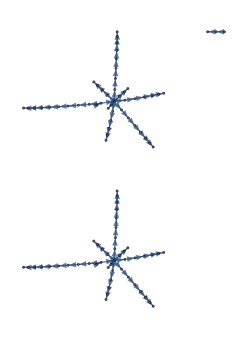

```mathematica
AdjacencyGraph[AtomList[atomMap],AtomToAtomAdjacencyMatrix[net,atomMap]]
```

Subgraphs for connected components

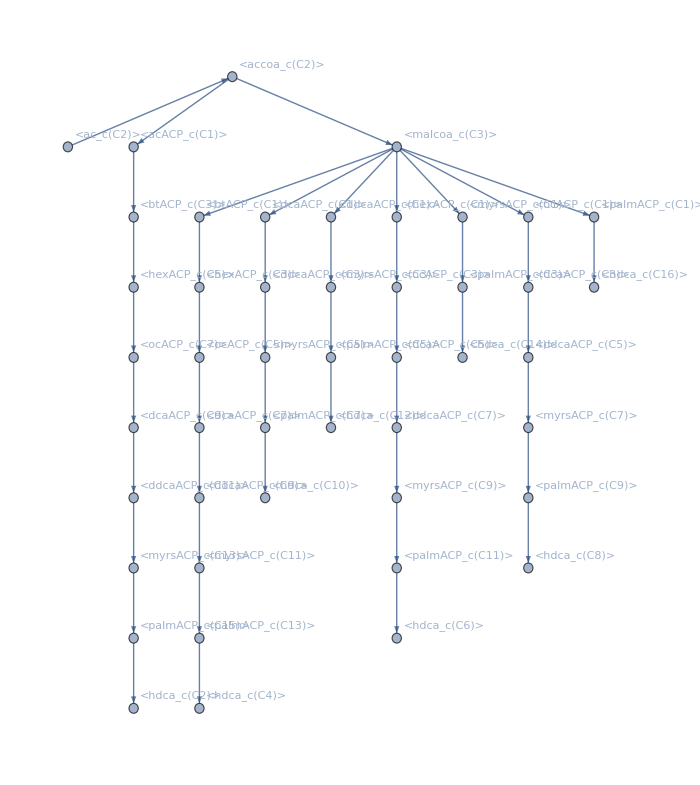
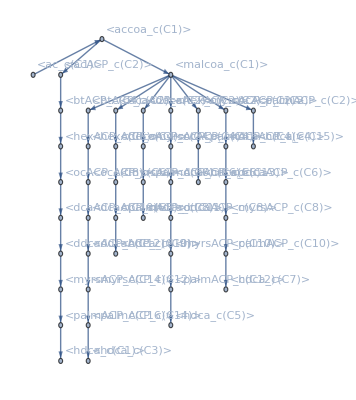
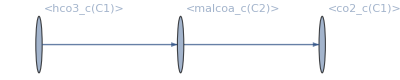

```mathematica
Block[{A,cl},
A=AdjacencyGraph[AtomList[atomMap],AtomToAtomAdjacencyMatrix[net,atomMap]];
cl=Cases[WeaklyConnectedComponents[A],c_List/;Length[c]>1];
Table[
Subgraph[A,c,VertexLabels->"Name"],
{c,cl}]]
```

## Specify input isotopomers (tracers)

```mathematica
<<NilssonLab`IsotopeDistributions`
```

Isotopomer distributions for substrates (tracers), one entry for each experiment

```mathematica
substrates=Cases[MetaboliteEMUs[bmap],EMU[Metabolite[_,"Input",_],__]]
```

{<ac_i{(12)}>,<hco3_i{(1)}>}

Labeled acetate

```mathematica
substrateDist=With[{p=1.0},
substrates/.{
e:EMU[m:Metabolite["ac",__],__]:>
Rule[m,EmpiricalIsotopomerDistribution[{{{Table[1,EMUSize[e]]},p},{{Table[0,EMUSize[e]]},1-p}}]],
e:EMU[met_Metabolite,__]:>Rule[met,EmpiricalIsotopomerDistribution[{{{Table[0,EMUSize[e]]},1.0}}]]}]
```

{Metabolite[ac,Input,Boundary]→EmpiricalIsotopomerDistribution[{{{{1,1}},1.},{{{0,0}},0.}}],Metabolite[hco3,Input,Boundary]→EmpiricalIsotopomerDistribution[{{{{0}},1.}}]}

## Generate EMU model

The EMU system is the same for stationary (steady-state) and nonstationary analysis.

We generate a carbon-only EMU network by specifying only carbon fragments as targets

```mathematica
targets=MetaboliteEMUs[atomMap]
```

{<ac_c{(12)}>,<acACP_c{(12)}>,<accoa_c{(12)}>,<btACP_c{(1234)}>,<co2_c{(1)}>,<dcaACP_c{(123456789a)}>,<ddcaACP_c{(123456789abc)}>,<hco3_c{(1)}>,<hdca_c{(123456789abcdefg)}>,<hexACP_c{(123456)}>,<malcoa_c{(123)}>,<myrsACP_c{(123456789abcde)}>,<ocACP_c{(12345678)}>,<palmACP_c{(123456789abcdefg)}>}

### EMU decomposition

This generates a set of EMU reactions. No symmetry in this case

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,Identity];
Length[emuReactions]
```

22

For a specific product

```mathematica
Cases[emuReactions,EMUReaction[_,_,EMU[Metabolite["succ",__],{{{1}}}],__]]//TableForm
```

{}

```mathematica
Cases[emuReactions,EMUReaction[_,_,EMU[Metabolite["cit","Mitochondria",_],__],__]]//TableForm
```

{}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

16

Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 3 internals, 1 substrates, 0 condensations >
2 | <EMUEquation (2), 4 internals, 1 substrates, 0 condensations >
3 | <EMUEquation (3), 1 internals, 0 substrates, 1 condensations >
4 | <EMUEquation (4), 1 internals, 0 substrates, 1 condensations >
5 | <EMUEquation (6), 1 internals, 0 substrates, 1 condensations >
6 | <EMUEquation (8), 1 internals, 0 substrates, 1 condensations >
7 | <EMUEquation (10), 1 internals, 0 substrates, 1 condensations >
8 | <EMUEquation (12), 1 internals, 0 substrates, 1 condensations >
9 | <EMUEquation (14), 1 internals, 0 substrates, 1 condensations >
10 | <EMUEquation (16), 2 internals, 0 substrates, 1 condensations >

Total number of isotopomer variables in the equation system

```mathematica
Total[Map[(Times@@#&),(Dimensions/@emus)+1]]
```

116

### Substrate EMUs

Calculate MIDs for network substrate EMUs

```mathematica
EMUMassIsotopomerDistribution[e_EMU,isoDist_]:=
Block[{a,ml},
(* arbitrarily pick first member of equiv. class *)
a=First[AtomNumbers[e]];
(* list of masses of the EMU *)
ml=Tuples[Map[Range[0,Length[#]]&,a]];
Table[
PDF[MarginalizeToMID[FragmentIsotopomerDistribution[isoDist,a]],x],
{x,ml}]]
```

```mathematica
irList={Table[
Rule[e,EMUMassIsotopomerDistribution[e,Metabolite[e]/.substrateDist]],
{e,Flatten[SubstrateEMUs/@emuEq]}]}
```

{{<hco3_i{(1)}>→{1.,0.},<ac_i{(12)}>→{0.,0.,1.}}}

## Simulate steady-state mass isotopomer data

```mathematica
<<NilssonLab`EMUTracing`
```

```mathematica
TableForm[
Round[EMUFluxMap[net][trueFlux],0.01],
TableHeadings->{EMUFluxMap[net,"reactions"],None}]
```

ac_IN | 8.
energy_IN | 23.
h2o_IN | 0.
h_IN | 42.
hco3_IN | 7.
ACCOAC_f | 7.
ACOATA_f | 1.
ACS_f | 8.
ADK1_f | 8.
CELLWORK_f | 23.
FA160ACPH_f | 1.
FAS100ACP_f | 1.
FAS120ACP_f | 1.
FAS140ACP_f | 1.
FAS160ACP_f | 1.
FAS40ACP_f | 1.
FAS60ACP_f | 1.
FAS80ACP_f | 1.
NADPH_REDOX_f | 14.
PPA_f | 8.

```mathematica
emuSol=EMUSimulate[emuEq,irList⟦1⟧,EMUFluxMap[net][trueFlux]]
```

<EMUSolution, 10 subsystems>

```mathematica
TableForm[emuSol/@targets,TableHeadings->{targets,None}]
```

<ac_c{(12)}> | 0. | 0. | 1. |  |  |  |  |  |  |  |  |  |  |  |  |  | 
<acACP_c{(12)}> | 0. | 0. | 1. |  |  |  |  |  |  |  |  |  |  |  |  |  | 
<accoa_c{(12)}> | 0. | 0. | 1. |  |  |  |  |  |  |  |  |  |  |  |  |  | 
<btACP_c{(1234)}> | 0. | 0. | 0. | 0. | 1. |  |  |  |  |  |  |  |  |  |  |  | 
<co2_c{(1)}> | 1. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
<dcaACP_c{(123456789a)}> | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. |  |  |  |  |  | 
<ddcaACP_c{(123456789abc)}> | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. |  |  |  | 
<hco3_c{(1)}> | 1. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
<hdca_c{(123456789abcdefg)}> | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
<hexACP_c{(123456)}> | 0. | 0. | 0. | 0. | 0. | 0. | 1. |  |  |  |  |  |  |  |  |  | 
<malcoa_c{(123)}> | 0. | 0. | 1. | 0. |  |  |  |  |  |  |  |  |  |  |  |  | 
<myrsACP_c{(123456789abcde)}> | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. |  | 
<ocACP_c{(12345678)}> | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. |  |  |  |  |  |  |  | 
<palmACP_c{(123456789abcdefg)}> | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.

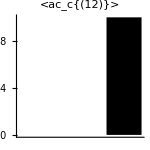
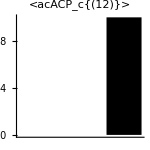
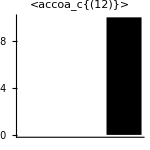
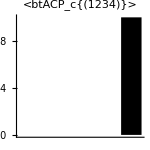
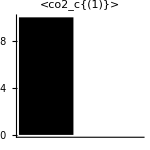
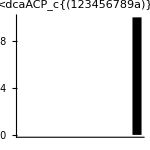
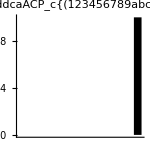
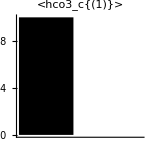

```mathematica
Table[
SimpleBarChart[emuSol[e],PlotLabel->e,AspectRatio->1,ImageSize->150],
{e,targets}]
```

## Nonstationary simulation

```mathematica
<<NilssonLab`EMUTracing`
```

Here, all MI fractions are time-dependent variables, and each internal EMU is associate with a differential equation over time rather than an algebraic equation. The condensations are the same, but also time dependent.

In tensor form, the steady state equation is A v X + B v Y + C v Z - D v X = 0  <--> (A-D) v X = - B v Y - C v Z
The nonstationary version is 
T * dX/dt = A v X(t) + B b Y + C v Z(t) - D v X(t)
where T is a diagnonal matrix of concentrations for each metabolite (same for all EMUs from that metabolite)

### Generate EMU diff equations

Define concentrations for each metabolite

```mathematica
metaboliteConc=Thread[Metabolites[net]->1.0];
```

```mathematica
emuDiffEqn=EMUDiffEquation[emuEq,x,t,irList⟦1⟧,EMUFluxMap[net][trueFlux],Map[Metabolite,InternalEMUs/@emuEq,{2}]/.metaboliteConc];
```

```mathematica
Dimensions/@emuDiffEqn
```

{{3,2},{4,3},{1,4},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{2,17}}

```mathematica
Length[Flatten[emuDiffEqn]]
```

116

### Simulate system

```mathematica
variables=Table[
x[e,j],
{eq,emuEq},{e,InternalEMUs[eq]},{j,0,EMUSize[First[InternalEMUs[eq]]]}];
```

```mathematica
Dimensions/@variables
```

{{3,2},{4,3},{1,4},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{2,17}}

We will need an initial MID state. Here we take the unlabeled state, so that x[e, j] is the unit vector

```mathematica
initial=Table[
x[e,j][0]==If[j==0,1,0],
{eq,emuEq},{e,InternalEMUs[eq]},{j,0,EMUSize[First[InternalEMUs[eq]]]}];
```

```mathematica
Dimensions/@initial
```

{{3,2},{4,3},{1,4},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{2,17}}

Simulation with NDSolve

```mathematica
tFinal=30.0;
```

```mathematica
sol=variables/.First[NDSolve[
Join[Flatten[emuDiffEqn],Flatten[initial]],
Flatten[variables],{t,0,tFinal}]];//AbsoluteTiming
```

{0.0275454,Null}

```mathematica
Dimensions/@sol
```

{{3,2},{4,3},{1,4},{1,5},{1,7},{1,9},{1,11},{1,13},{1,15},{2,17}}

EMU variables per metabolite

```mathematica
Table[Count[Flatten[variables],x[EMU[m,__],_]],{m,Metabolites[net]}]
```

{3,3,3,0,0,0,0,5,2,0,11,13,0,0,0,2,17,7,9,15,0,0,9,17,0,0}

### All solutions

```mathematica
(*Plot[Table[f[t],{f,Flatten[sol]}],{t,0,2}]*)
```

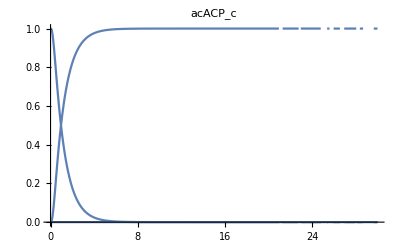
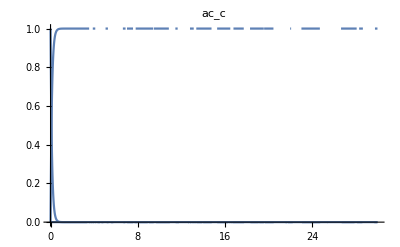
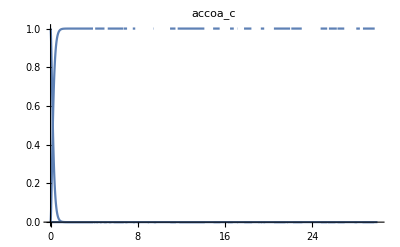
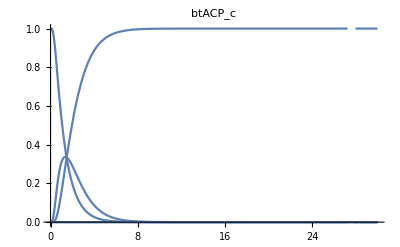
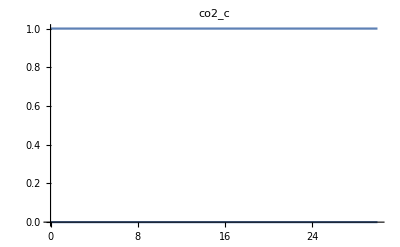
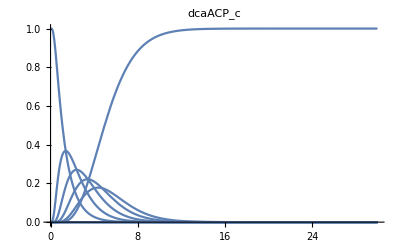
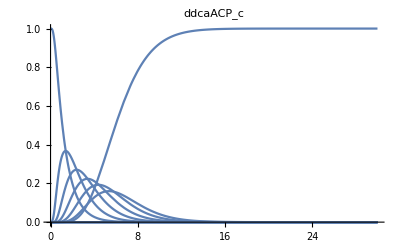
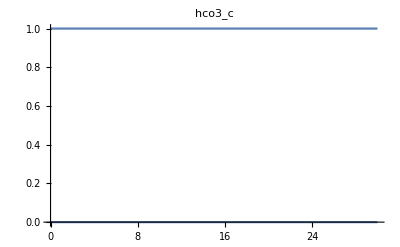

```mathematica
Block[{fl},
Table[
fl=Extract[sol,Position[variables,x[EMU[m,__],_]]];
If[Length[fl]>0,
Plot[Table[f[t],{f,Flatten[fl]}],{t,0,tFinal},PlotRange->{0,1},PlotLabel->MetaboliteShortName[m]],
{}],
{m,Metabolites[net]}]]//Flatten
```

### All targets

```mathematica
(*Plot[Table[f[t],{f,Flatten[sol]}],{t,0,2}]*)
```

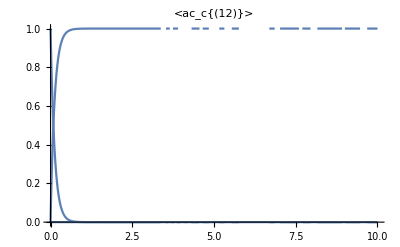
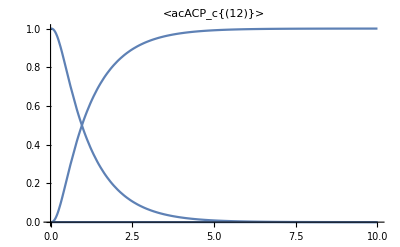
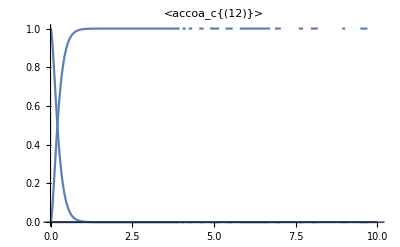
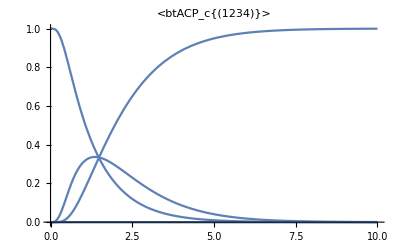
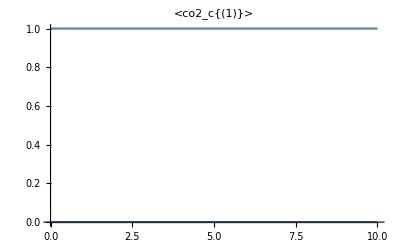
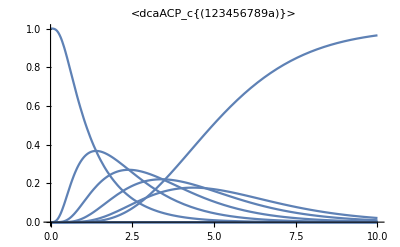
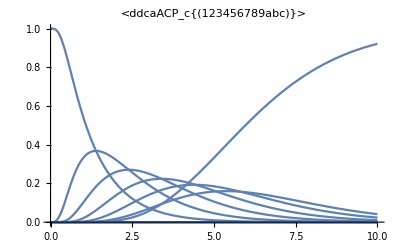
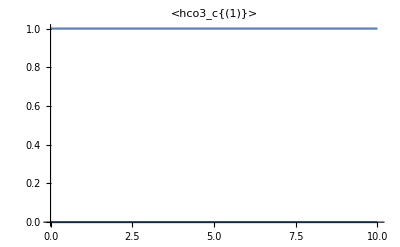

```mathematica
Block[{fl},
Table[
fl=Extract[sol,Position[variables,x[emu,_]]];
Plot[Table[f[t],{f,Flatten[fl]}],{t,0,10},PlotRange->{0,1},PlotLabel->emu],
{emu,targets}]]//Flatten
```

### Fully labeled MIs

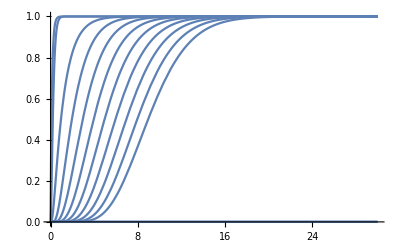

```mathematica
Block[{ix,functions,vars},
ix=Position[
variables,
Alternatives@@Table[x[emu,EMUSize[emu]],{emu,targets}]];
functions=Extract[sol,ix];
vars=Extract[variables,ix];
Plot[
Table[functions⟦i⟧[t],{i,Length[vars]}],
{t,0,tFinal},PlotLegends->Automatic]]
```

### Specific metabolites

#### Palmitate

Metabolite EMUs (mass isotopomers)

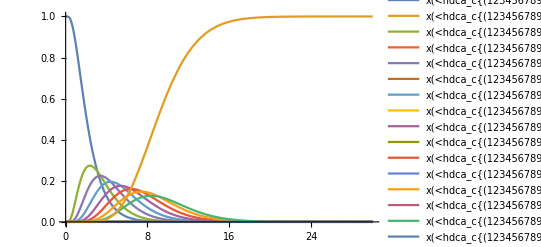

```mathematica
Block[{ix,fl,vl},
ix=Position[variables,x[EMU[Metabolite["hdca","Cytosol",_],_],_]];
fl=Extract[sol,ix];
vl=Extract[variables,ix];
Plot[
Evaluate[Table[Tooltip[fl⟦i⟧[t],vl⟦i⟧],{i,Length[ix]}]],
{t,0,tFinal},PlotRange->{0,1},PlotLegends->vl]]
```

### End point, compare with steady state solution

```mathematica
MetaboliteEMUs[atomMap]
```

{<ac_c{(12)}>,<acACP_c{(12)}>,<accoa_c{(12)}>,<btACP_c{(1234)}>,<co2_c{(1)}>,<dcaACP_c{(123456789a)}>,<ddcaACP_c{(123456789abc)}>,<hco3_c{(1)}>,<hdca_c{(123456789abcdefg)}>,<hexACP_c{(123456)}>,<malcoa_c{(123)}>,<myrsACP_c{(123456789abcde)}>,<ocACP_c{(12345678)}>,<palmACP_c{(123456789abcdefg)}>}

Discrepancy due to epsilon flux through “zero” reactions -- should remove these

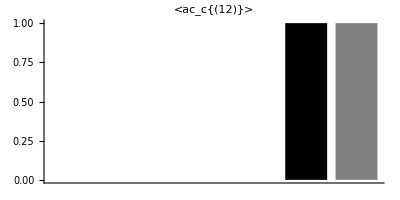
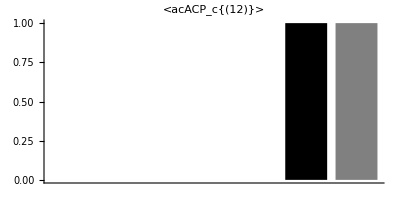
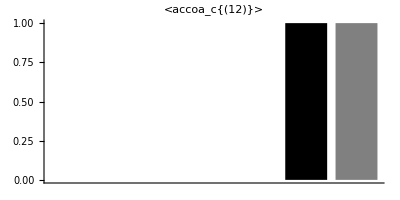
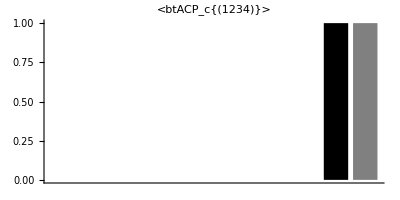
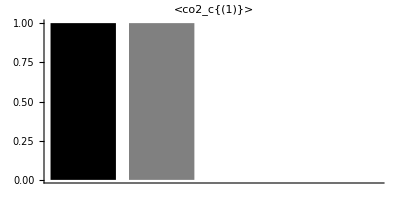
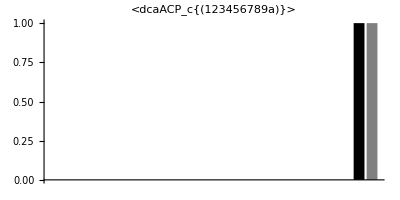
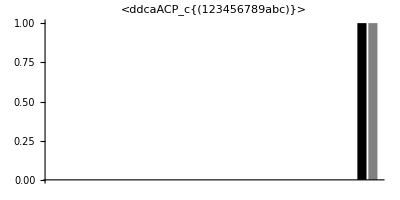
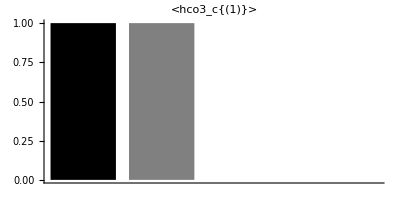

```mathematica
Block[{ix,fl},
Table[
ix=Position[variables,x[e,_]];
fl=Extract[sol,ix];
SimpleBarChart[
Transpose[{Evaluate[Table[f[tFinal],{f,fl}]],emuSol[e]}],
AspectRatio->1/2,PlotLabel->e],
{e,MetaboliteEMUs[atomMap]}]]
```

### Sample time points

```mathematica
timePoints={2.5,5,7.5,10,20};
```

```mathematica
samples=Block[{ix,functions},
Transpose[
Table[
ix=Position[variables,x[emu,_]];
functions=Extract[sol,ix];
Table[f[t],{t,timePoints},{f,functions}],
{emu,targets}]]];
```

```mathematica
Dimensions[samples]
```

{5,14}

Save as MI data set

```mathematica
fileName="C:\\Users\\rolnil\\OneDrive - KI.SE\\Lab common\\projects\\reverse-engineering-deniz\\reverse-engineering\\Data\\simulation\\fatty-acid-synthesis\\fatty-acid-synthesis-nonstationary.tsv"
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\fatty-acid-synthesis\fatty-acid-synthesis-nonstationary.tsv

```mathematica
Export[
fileName,
Block[{mi,met},
met=Flatten[Table[MetaboliteShortName[Metabolite[e]],{e,targets},{i,0,EMUSize[e]}]];
mi=Flatten[Table[Range[0,EMUSize[e]],{e,targets}]];
ArrayFlatten[
{{{{"Metabolite","MI"}},{timePoints}},
{Transpose[{met,mi}],Transpose[Flatten/@samples]}}]]
]
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\fatty-acid-synthesis\fatty-acid-synthesis-nonstationary.tsv